# ϕ^2 spectral density for free massive scalar field (Fig 7)

#### Kernels for spectral density and integrated spectral densities

```mathematica
f0[x_,x0_]:= HeavisideTheta[x-x0];
f1[x_,x0_]:= (x-x0) HeavisideTheta[x-x0];
f2[x_,x0_]:=1/2 (x-x0)^2 HeavisideTheta[x-x0];

f3[x_,x0_]:=1/(3!) (x-x0)^3 HeavisideTheta[x-x0];

f4[x_,x0_]:=1/(4!) (x-x0)^4 HeavisideTheta[x-x0];
```

#### Exact one-loop result for ρ_(ϕ^2) and its integrals, and for ρ_(T_(--))

```mathematica
ρBosonLoop[μsq_]=1/(π √(μsq(μsq-4)));
ρTmmBosonLoop[μsq_]=1/(π √(μsq^5(μsq-4)));
Iϕsq0[μsq_]=Assuming[μsq>4,Integrate[ρBosonLoop[μsqp],{μsqp,4,μsq}]//FullSimplify]
Iϕsq1[μsq_]=Assuming[μsq>4,Integrate[(μsq-μsqp)ρBosonLoop[μsqp],{μsqp,4,μsq}]//FullSimplify]

ITmmsq0[μsq_]=Assuming[μsq>4,Integrate[ρTmmBosonLoop[μsqp],{μsqp,4,μsq}]//FullSimplify]
```

(2 Log[1+√((-4+μsq)/μsq)]+Log[μsq/4])/π

(-√((-4+μsq) μsq)+Log[16]+2 (-2+μsq) Log[1+√((-4+μsq)/μsq)]+μsq Log[μsq/4]-2 Log[μsq])/π

(2 √((-4+μsq) μsq)+√((-4+μsq) μsq^3))/(12 π μsq^2)

#### Overlap ⟨ϕ^2(0)|[ϕϕ]_l,p ⟩ of two-particle primary states and ϕ^2(0)

```mathematica
BosonOverlap[l_]:=√(2/π)√((3+2l)/((1+l)(2+l)));
```

#### Mass term matrix elements (M_(l l'))^(ϕ^2)

```mathematica
Boson2ϕMassMatrix[l_,lp_]:= 2 √(((3+2 m) (1+n) (2+n) (3+2 n))/((1+m) (2+m)))/.{n->Min[l,lp],m->Max[l,lp]};
```

#### Put it all together

Choose truncation

```mathematica
LMaxJacobi=20;myPrecision=$MachinePrecision;
```

Construct Hamiltonian

```mathematica
MϕϕJacobi=Outer[Boson2ϕMassMatrix[#1,#2]&,Range[0,LMaxJacobi,2],Range[0,LMaxJacobi,2]];
```

Diagonalize Hamiltonian

```mathematica
JacobiϕϕMassEvecs=Eigenvectors[SetPrecision[MϕϕJacobi,myPrecision]]//Reverse//Transpose;
JacobiϕϕMassEvals=Eigenvalues[SetPrecision[MϕϕJacobi,myPrecision]]//Reverse;
```

Look at overlap over operator with energy eigenstates

```mathematica
JacobiϕϕOverlap=BosonOverlap/@Range[0,LMaxJacobi,2]//SetPrecision[#,myPrecision]&;
JacobiTmmOverlap=If[#==0,√(1/(12π)),0]&/@Range[0,LMaxJacobi,2]//SetPrecision[#,myPrecision]&;
JacobiϕϕOverlapMassBasis=JacobiϕϕOverlap.JacobiϕϕMassEvecs;
JacobiTmmOverlapMassBasis=JacobiTmmOverlap.JacobiϕϕMassEvecs;
```

Sum over states to get spectral density and integrated spectral density

```mathematica
totalstates=Length[JacobiϕϕMassEvecs];
IϕsqJacobi0[μsq_]=Sum[JacobiϕϕOverlapMassBasis[[i]]^2 f0[μsq,JacobiϕϕMassEvals[[i]]],{i,totalstates}];
IϕsqJacobi1[μsq_]=Sum[JacobiϕϕOverlapMassBasis[[i]]^2 f1[μsq,JacobiϕϕMassEvals[[i]]],{i,totalstates}];

ITmmJacobi0[μsq_]=Sum[JacobiTmmOverlapMassBasis[[i]]^2 f0[μsq,JacobiϕϕMassEvals[[i]]],{i,totalstates}];
```

Fig 7, left plot

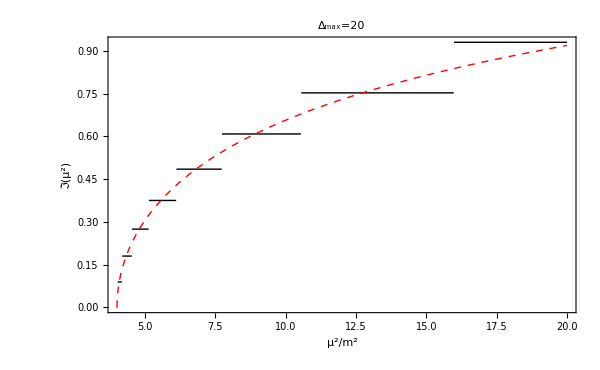

```mathematica
p20=Plot[{IϕsqJacobi0[a],Iϕsq0[a]},{a,4,20},Frame->True,BaseStyle->{FontFamily->"Palatino",FontSize->18},PlotStyle->{{Black,Thick},{Red,Thick,Dashed}},ImageSize->600,FrameLabel->{"μ^2/m^2","ℑ(μ^2)"},PlotLabel->"Δ_max="<>ToString[LMaxJacobi],RotateLabel->False]
```

Extra integrated ϕ^2

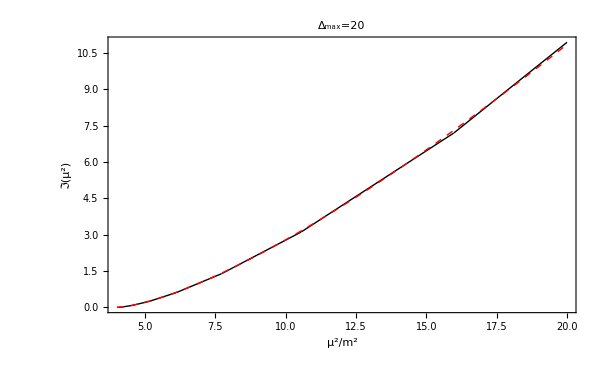

```mathematica
pI20=Plot[{IϕsqJacobi1[a],Iϕsq1[a]},{a,4,20},Frame->True,BaseStyle->{FontFamily->"Palatino",FontSize->18},PlotStyle->{{Black,Thick},{Red,Thick,Dashed}},ImageSize->600,FrameLabel->{"μ^2/m^2","ℑ(μ^2)"},PlotLabel->"Δ_max="<>ToString[LMaxJacobi],RotateLabel->False]
```

C function

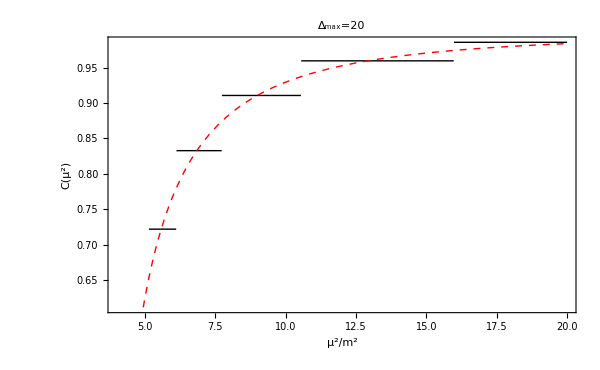

```mathematica
pCfn20=Plot[{12π ITmmJacobi0[a],12π ITmmsq0[a]},{a,4,20},Frame->True,BaseStyle->{FontFamily->"Palatino",FontSize->18},PlotStyle->{{Black,Thick},{Red,Thick,Dashed}},ImageSize->600,FrameLabel->{"μ^2/m^2","C(μ^2)"},PlotLabel->"Δ_max="<>ToString[LMaxJacobi],RotateLabel->False]
```

Redo it at higher truncation

```mathematica
LMaxJacobi=100;myPrecision=$MachinePrecision;
MϕϕJacobi=Outer[Boson2ϕMassMatrix[#1,#2]&,Range[0,LMaxJacobi,2],Range[0,LMaxJacobi,2]];
JacobiϕϕMassEvecs=Eigenvectors[SetPrecision[MϕϕJacobi,myPrecision]]//Reverse//Transpose;
JacobiϕϕMassEvals=Eigenvalues[SetPrecision[MϕϕJacobi,myPrecision]]//Reverse;
JacobiϕϕOverlap=BosonOverlap/@Range[0,LMaxJacobi,2]//SetPrecision[#,myPrecision]&;
JacobiTmmOverlap=If[#==0,√(1/(12π)),0]&/@Range[0,LMaxJacobi,2]//SetPrecision[#,myPrecision]&;
JacobiϕϕOverlapMassBasis=JacobiϕϕOverlap.JacobiϕϕMassEvecs;
JacobiTmmOverlapMassBasis=JacobiTmmOverlap.JacobiϕϕMassEvecs;



totalstates=Length[JacobiϕϕMassEvecs];
IϕsqJacobi0[μsq_]=Sum[JacobiϕϕOverlapMassBasis[[i]]^2 f0[μsq,JacobiϕϕMassEvals[[i]]],{i,totalstates}];
IϕsqJacobi1[μsq_]=Sum[JacobiϕϕOverlapMassBasis[[i]]^2 f1[μsq,JacobiϕϕMassEvals[[i]]],{i,totalstates}];

ITmmJacobi0[μsq_]=Sum[JacobiTmmOverlapMassBasis[[i]]^2 f0[μsq,JacobiϕϕMassEvals[[i]]],{i,totalstates}];
```

Fig 7, right plot

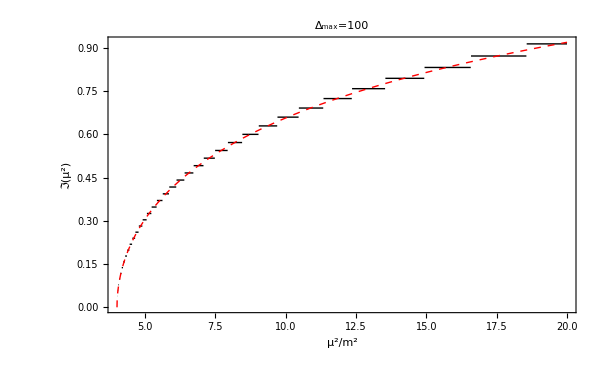

```mathematica
p100=Plot[{IϕsqJacobi0[a],Iϕsq0[a]},{a,4,20},Frame->True,BaseStyle->{FontFamily->"Palatino",FontSize->18},PlotStyle->{{Black,Thick},{Red,Thick,Dashed}},ImageSize->600,FrameLabel->{"μ^2/m^2","ℑ(μ^2)"},PlotLabel->"Δ_max="<>ToString[LMaxJacobi],RotateLabel->False]
```

C function

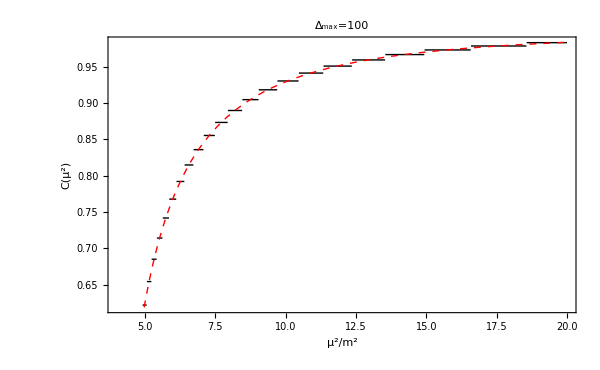

```mathematica
pCfn100=Plot[{12π ITmmJacobi0[a],12π ITmmsq0[a]},{a,4,20},Frame->True,BaseStyle->{FontFamily->"Palatino",FontSize->18},PlotStyle->{{Black,Thick},{Red,Thick,Dashed}},ImageSize->600,FrameLabel->{"μ^2/m^2","C(μ^2)"},PlotLabel->"Δ_max="<>ToString[LMaxJacobi],RotateLabel->False]
```

#### Δ_max=40

```mathematica
LMaxJacobi=40;myPrecision=$MachinePrecision;
MϕϕJacobi=Outer[Boson2ϕMassMatrix[#1,#2]&,Range[0,LMaxJacobi,2],Range[0,LMaxJacobi,2]];
JacobiϕϕMassEvecs=Eigenvectors[SetPrecision[MϕϕJacobi,myPrecision]]//Reverse//Transpose;
JacobiϕϕMassEvals=Eigenvalues[SetPrecision[MϕϕJacobi,myPrecision]]//Reverse;
JacobiϕϕOverlap=BosonOverlap/@Range[0,LMaxJacobi,2]//SetPrecision[#,myPrecision]&;
JacobiTmmOverlap=If[#==0,√(1/(12π)),0]&/@Range[0,LMaxJacobi,2]//SetPrecision[#,myPrecision]&;
JacobiϕϕOverlapMassBasis=JacobiϕϕOverlap.JacobiϕϕMassEvecs;
JacobiTmmOverlapMassBasis=JacobiTmmOverlap.JacobiϕϕMassEvecs;



totalstates=Length[JacobiϕϕMassEvecs];
IϕsqJacobi0[μsq_]=Sum[JacobiϕϕOverlapMassBasis[[i]]^2 f0[μsq,JacobiϕϕMassEvals[[i]]],{i,totalstates}];
IϕsqJacobi1[μsq_]=Sum[JacobiϕϕOverlapMassBasis[[i]]^2 f1[μsq,JacobiϕϕMassEvals[[i]]],{i,totalstates}];

ITmmJacobi0[μsq_]=Sum[JacobiTmmOverlapMassBasis[[i]]^2 f0[μsq,JacobiϕϕMassEvals[[i]]],{i,totalstates}];
```

Integrated ρ_(ϕ^2)

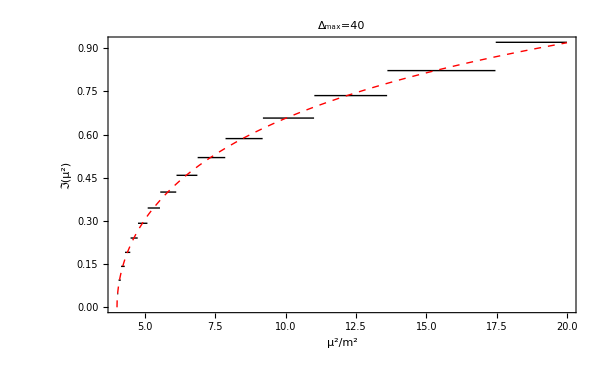

```mathematica
p40=Plot[{IϕsqJacobi0[a],Iϕsq0[a]},{a,4,20},Frame->True,BaseStyle->{FontFamily->"Palatino",FontSize->18},PlotStyle->{{Black,Thick},{Red,Thick,Dashed}},ImageSize->600,FrameLabel->{"μ^2/m^2","ℑ(μ^2)"},PlotLabel->"Δ_max="<>ToString[LMaxJacobi],RotateLabel->False]
```

C function

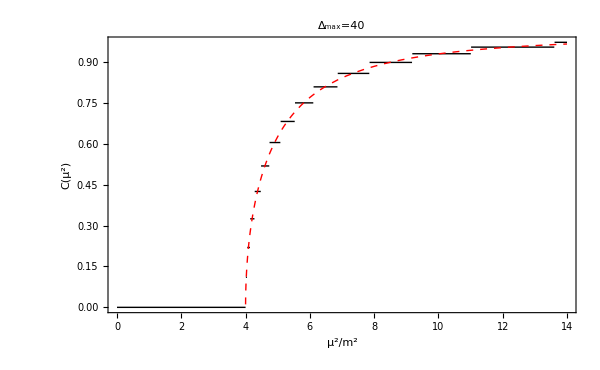

```mathematica
pC40=Plot[{12π ITmmJacobi0[a],12π ITmmsq0[a]},{a,0,14},Frame->True,BaseStyle->{FontFamily->"Palatino",FontSize->18},PlotStyle->{{Black,Thick},{Red,Thick,Dashed}},ImageSize->600,FrameLabel->{"μ^2/m^2","C(μ^2)"},PlotLabel->"Δ_max="<>ToString[LMaxJacobi],RotateLabel->False]
```

#### Δ_max=500 (takes about a minute)

```mathematica
LMaxJacobi=500;myPrecision=$MachinePrecision;
MϕϕJacobi=Outer[Boson2ϕMassMatrix[#1,#2]&,Range[0,LMaxJacobi,2],Range[0,LMaxJacobi,2]];
JacobiϕϕMassEvecs=Eigenvectors[SetPrecision[MϕϕJacobi,myPrecision]]//Reverse//Transpose;
JacobiϕϕMassEvals=Eigenvalues[SetPrecision[MϕϕJacobi,myPrecision]]//Reverse;
JacobiϕϕOverlap=BosonOverlap/@Range[0,LMaxJacobi,2]//SetPrecision[#,myPrecision]&;
JacobiTmmOverlap=If[#==0,√(1/(12π)),0]&/@Range[0,LMaxJacobi,2]//SetPrecision[#,myPrecision]&;
JacobiϕϕOverlapMassBasis=JacobiϕϕOverlap.JacobiϕϕMassEvecs;
JacobiTmmOverlapMassBasis=JacobiTmmOverlap.JacobiϕϕMassEvecs;



totalstates=Length[JacobiϕϕMassEvecs];
IϕsqJacobi0[μsq_]=Sum[JacobiϕϕOverlapMassBasis[[i]]^2 f0[μsq,JacobiϕϕMassEvals[[i]]],{i,totalstates}];
IϕsqJacobi1[μsq_]=Sum[JacobiϕϕOverlapMassBasis[[i]]^2 f1[μsq,JacobiϕϕMassEvals[[i]]],{i,totalstates}];

ITmmJacobi0[μsq_]=Sum[JacobiTmmOverlapMassBasis[[i]]^2 f0[μsq,JacobiϕϕMassEvals[[i]]],{i,totalstates}];
```

Integrated ρ_(ϕ^2)

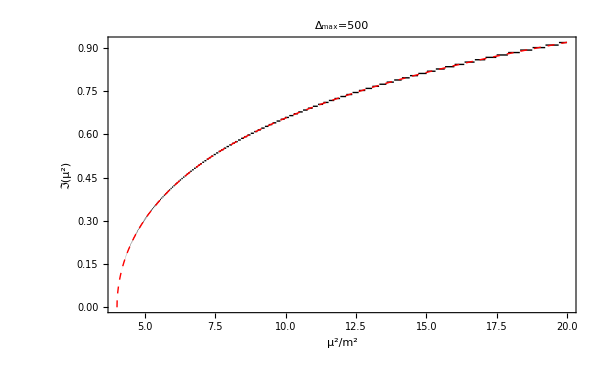

```mathematica
p500=Plot[{IϕsqJacobi0[a],Iϕsq0[a]},{a,4,20},Frame->True,BaseStyle->{FontFamily->"Palatino",FontSize->18},PlotStyle->{{Black,Thick},{Red,Thick,Dashed}},ImageSize->600,FrameLabel->{"μ^2/m^2","ℑ(μ^2)"},PlotLabel->"Δ_max="<>ToString[LMaxJacobi],RotateLabel->False]
```

C function

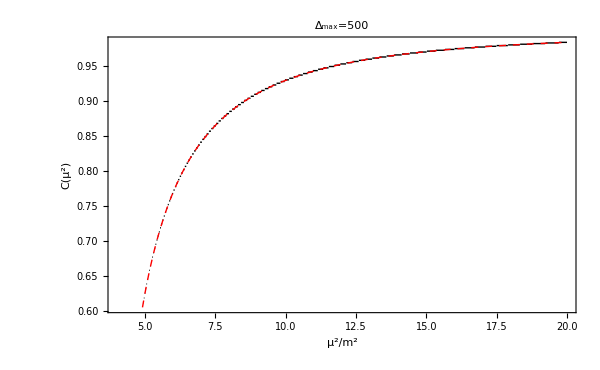

```mathematica
pC500=Plot[{12π ITmmJacobi0[a],12π ITmmsq0[a]},{a,4,20},Frame->True,BaseStyle->{FontFamily->"Palatino",FontSize->18},PlotStyle->{{Black,Thick},{Red,Thick,Dashed}},ImageSize->600,FrameLabel->{"μ^2/m^2","C(μ^2)"},PlotLabel->"Δ_max="<>ToString[LMaxJacobi],RotateLabel->False]
```